```mathematica
Quit[]
```

```mathematica
<<BBHpnToolkit`
```

Authors: Rickmoy Samanta(rickmoysamanta@gmail.com); Sashwat Tanay (sashwattanay@gmail.com, https://sashwattanay.github.io/sashwat_site/)

```mathematica
(*User input*)
m1=5/2  ;            (*bigger mass*)
m2=1    ;              (*smaller mass*)
(*G=1; μ= (m1 m2)/(m1+m2); M=m1+m2;*)

ϵ=1./100         (* This is 1/c^2 *);
R=2{ 1,1,1};

P={1/2 ,-1/2,1/3};
(*L=Norm[ Cross[R,P]]*)
S1={0,1,1}√ϵ  ;              S2={1,-3/10,0}√ϵ;   

(*S1 and S2 (with √ϵ included) are the spin angular momenta of the two black holes. Their dimension is same as that of orbital angular momentum L = R x P. *)
```

```mathematica
(*Solve[R.P==0,x] (* x chosen to make quasi-circular orbit*)*)
(*eng=(Norm[P])^2/(2 μ)-(G M μ)/Norm[R]*)
```

# parameter estimates

```mathematica
eng= frequency[m1,m2,R,P,S1,S2,ϵ][[1]]
pnparam=(Norm[P]/(m1 m2/(m1+m2)))^2 ϵ
Gc=1; a=(-Gc  m1 m2)/(2 eng);
tp=2 π( a^3/(Gc (m1+m2)))^(1/2)
tp/(pnparam)^1
```

-0.30455

0.0119778

27.9269

2331.56

# Frequencies

```mathematica
freqArr= frequency[m1,m2,R,P,S1,S2,ϵ][[2]]            (*The 5 frequencies (within the action-angle framework) of the system*)
```

{0.00104211,0.,0.226427,0.221494,0.00137152}

# BBH system at a later time

```mathematica
(*State of the system at time = tf. We are giving {R,P,S1,S2}*)        

NmHflow[m1,m2,R,P,S1,S2,tf  ,ϵ]                   (*got via numerical integration of Hamilton's equations*)  
Acflow[m1,m2,R,P,S1,S2,tf  ,ϵ]
(*got from the action-angle-based closed-form solution as given in arXiv:2110.15351 and arXiv:2012.06586 *)
                     
Hflow[m1,m2,R,P,S1,S2,tf  ,ϵ]     
(*got from the closed-form solution via integrating the Hamilton's equations as in arXiv:1908.02927 (with 1PN effects added)*)
```

{{2.20314,-4.19308,1.06083},{-0.271905,-0.355952,-0.323436},{0.0609223,-0.0272928,0.124674},{-0.0280405,0.00650067,-0.100357}}

{{3.68215,-1.46397,2.9948},{0.00642687,-0.52522,-0.109807},{0.0609249,-0.0263804,0.124869},{-0.0279413,0.00614049,-0.100338}}

{{3.68215,-1.46397,2.9948},{0.00642729,-0.52522,-0.109807},{0.0609249,-0.0263807,0.124869},{-0.0279413,0.00614037,-0.100338}}

```mathematica
|
```

# error computation

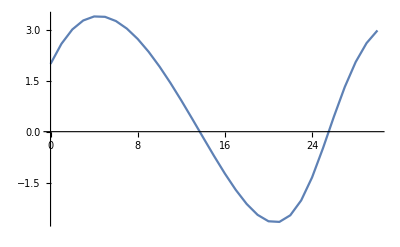

```mathematica
ListLinePlot[Table[{t,NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]][[1]]},{t,0,30,1}]]
```

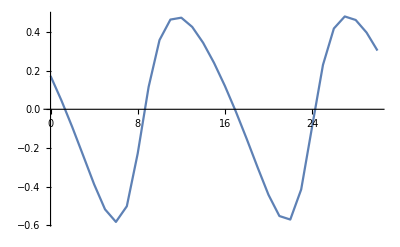

```mathematica
ListLinePlot[Table[{t,NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[2]][[1]]},{t,0,30,1}]]
```

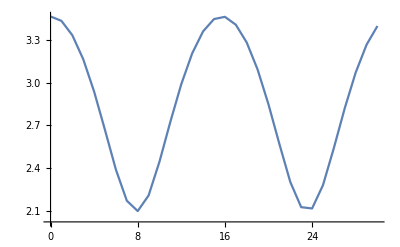

```mathematica
ListLinePlot[Table[{t,Norm[NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]]]},{t,0,30,1}]]
```

```mathematica
ListLinePlot[{Table[{t,NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[3]][[1]]},{t,0,6000,5}],Table[{t,Hflow[m1,m2,R,P,S1,S2,t ,ϵ][[3]][[1]]},{t,0,6000,5}]},
(*PlotStyle->{Blue,Red},*)AxesLabel->{Style["t'",Black,FontFamily->"Candara",FontSize->30],Style["S_1^x",Black,FontFamily->"Cambria",FontSize->30]},TicksStyle->Directive[Lighter[Black],FontSize->14],PlotLegends->Placed[{"Numerical","Analytical"},{.5,1}]]
```

-Graphics-

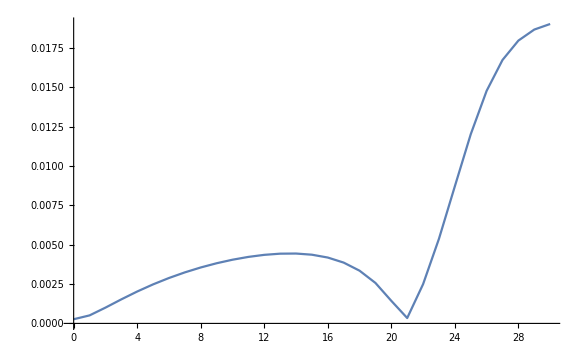

```mathematica
ListLinePlot[Table[{t,VectorAngle[NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]],Acflow[m1,m2,R,P,S1,S2,t  ,ϵ][[1]]]},{t,0,30,1}]]
```

```mathematica
VectorAngle[NmHflow[m1,m2,R,P,S1,S2,5 ,ϵ][[1]],Acflow[m1,m2,R,P,S1,S2,5  ,ϵ][[1]]]
```

0.00248094

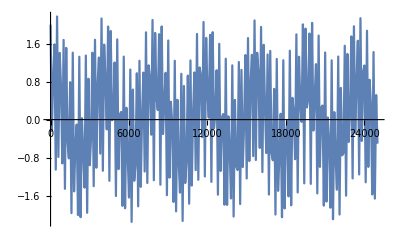

```mathematica
(*ϵ=1./1000 ;*)ListLinePlot[Table[{t,NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]][[1]]},{t,0,25000,100}]]
```

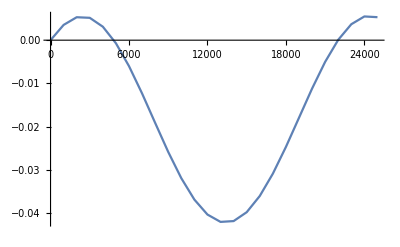

```mathematica
ListLinePlot[Table[{t,NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[3]][[1]]},{t,0,25000,1000}]]
```

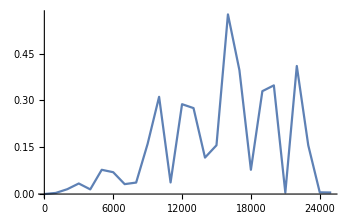

```mathematica
ListLinePlot[Table[{t,Abs[1-Norm[Acflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]]]/Norm[NmHflow[m1,m2,R,P,S1,S2,t  ,ϵ][[1]]]]},{t,0,25000,1000}]]
```